## This file used to be BC_FirstTryTOSS

```mathematica
WantDetails="NoWantDetails";
```

#### Choose Tmat, then check

```mathematica
Tmat=TmatIgel;
```

```mathematica
Tmat=TmatDefeat;
```

```mathematica
Tmat=TmatSSA2023;
```

```mathematica
Tmat=TmatMar17;
```

```mathematica
Tmat=TmatBrownTypo;
```

```mathematica
Tmat=TmatBrownNew;
```

```mathematica
Tmat==Transpose[Tmat]
MatrixNote[Tmat]
PrintVoigt[Tmat]
```

True

Tmat is TmatBrownNew

The [T]_𝔹𝔹 matrix is (50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)

The eigenvalues are: {204.263,179.169,75.8705,60.7101,50.1339,33.4538}

The Voigt matrix is (68.3 | 32.2 | 30.4 | 4.9 | -2.3 | -0.9
32.2 | 184.3 | 5. | -4.4 | -7.8 | -6.4
30.4 | 5. | 180. | -9.2 | 7.5 | -9.4
4.9 | -4.4 | -9.2 | 25. | -2.4 | -7.2
-2.3 | -7.8 | 7.5 | -2.4 | 26.9 | 0.6
-0.9 | -6.4 | -9.4 | -7.2 | 0.6 | 33.6)

10-7-2023 12:54

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 129.395   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.454 = 26.037^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

#### Choose TET-XISO path

```mathematica
Σn[0]=TRIV;
Σn[1]=MONO;
Σn[2]=ORTH;
Σn[3]=TET;
Σn[4]=XISO;
Σn[5]=ISO;
nMax=5;
Σn/@Range[0,nMax]
```

{TRIV,MONO,ORTH,TET,XISO,ISO}

#### Choose TRIG-CUBE path

```mathematica
Σn[0]=TRIV;
Σn[1]=MONO;
Σn[2]=TRIG;
Σn[3]=CUBE;
Σn[4]=ISO;
nMax=4;
Σn/@Range[0,nMax]
```

{TRIV,MONO,TRIG,CUBE,ISO}

```mathematica
ListΣ=Σn/@Range[0,nMax]
```

{TRIV,MONO,TRIG,CUBE,ISO}

#### OutputFor (Pathway 2)

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@Range[0,nMax]];
OutputFor[Tmat,Σn[#]]&/@Range[0,nMax]
```

Tmat is TmatBrownNew

Node sequence is {TRIV,MONO,TRIG,CUBE,ISO}

10-7-2023 12:54

𝒯_TRIV = 𝒯

d(T, 𝒯_TRIV) = d(T, 𝒯) = 0 for all elastic maps T

β_TRIV^T = ∠(T, 𝒯_TRIV) = 0           ''

10-7-2023 12:54

NMinimize = {19.3941,{θ→1.68223,σ→0.319894,ϕ→2.33199}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {96.4,0.,133.6})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0767049 | -0.993798 | -0.0805105
-0.68551 | -0.111201 | 0.719521
-0.724011 | 0 | -0.689788)  (A MONO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

10-7-2023 12:54

NMinimize = {82.3728,{θ→0.22904,σ→-0.867254,ϕ→1.33736}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TRIG(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {13.1,-49.7,76.6})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.318873 | 0.0249105 | 0.94747
-0.708665 | 0.670078 | 0.220885
-0.629376 | -0.741873 | 0.231323)  (A TRIG-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TRIG(U)))

10-7-2023 12:54

NMinimize = {106.21,{θ→0.0974921,σ→-1.53454,ϕ→1.66977}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_CUBE(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {5.6,-87.9,95.7})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.093709 | -0.101807 | 0.990381
-0.994946 | 0.0264644 | 0.0968614
-0.036071 | -0.994452 | -0.0988123)  (A CUBE-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_CUBE(U)))

10-7-2023 12:55

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 129.395   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.454 = 26.037^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

{Null,Null,Null,Null,Null}

#### OutputFor (Pathway 3) ClosestToPrevious[n, Tmat] has symmetry Σn[n].

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@Range[0,nMax]];
OutputFor[ClosestToPrevious[#,Tmat],Σn[#+1]]&/@Range[0,nMax-1]
```

Tmat is TmatBrownNew

Node sequence is {TRIV,MONO,TRIG,CUBE,ISO}

10-7-2023 12:55

NMinimize = {19.3941,{θ→1.68223,σ→0.319894,ϕ→2.33199}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {96.4,0.,133.6})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0767049 | -0.993798 | -0.0805105
-0.68551 | -0.111201 | 0.719521
-0.724011 | 0 | -0.689788)  (A MONO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

10-7-2023 12:55

NMinimize = {81.7126,{θ→0.29446,σ→0.268627,ϕ→1.38203}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TRIG(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {16.9,15.4,79.2})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0961012 | -0.327473 | 0.939961
0.30649 | 0.908185 | 0.285067
-0.94701 | 0.260693 | 0.187645)  (A TRIG-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TRIG(U)))

10-7-2023 12:55

NMinimize = {75.8243,{θ→1.19125,σ→-0.437035,ϕ→0.824001}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_CUBE(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {68.3,-25.,47.2})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.621153 | -0.735012 | 0.271895
0.414832 | 0.602724 | 0.681644
-0.664894 | -0.310614 | 0.67929)  (A CUBE-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_CUBE(U)))

10-7-2023 12:56

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 62.7752   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.233 = 13.33^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

{Null,Null,Null,Null}

#### Elastic maps at the nodes on Pathway 2

```mathematica
SmatOfN[n_,pw2]:=Closest[Tmat,Σn[n]];
```

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@Range[0,nMax]];
Chop[MatrixForm[SmatOfN[#,pw2]],0.0001]&/@Range[0,nMax]
```

Tmat is TmatBrownNew

Node sequence is {TRIV,MONO,TRIG,CUBE,ISO}

{(50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267),(48.5015 | -10.1159 | -7.74458 | -9.22251 | 9.37601 | -7.38876
-10.1159 | 61.7123 | 0.910195 | -8.9761 | -11.3441 | -3.2773
-7.74458 | 0.910195 | 59.1615 | -3.40581 | 4.3541 | -12.0748
-9.22251 | -8.9761 | -3.40581 | 96.5977 | 48.3338 | 35.6995
9.37601 | -11.3441 | 4.3541 | 48.3338 | 148.36 | -21.2519
-7.38876 | -3.2773 | -12.0748 | 35.6995 | -21.2519 | 189.267),(86.1583 | -20.7848 | -27.4637 | -18.0406 | 7.28212 | -3.65734
-20.7848 | 63.5007 | 17.858 | -2.53608 | -10.5831 | -15.6879
-27.4637 | 17.858 | 70.0111 | 7.84699 | 2.43911 | -14.98
-18.0406 | -2.53608 | 7.84699 | 81.7222 | 21.7491 | 30.3818
7.28212 | -10.5831 | 2.43911 | 21.7491 | 112.941 | -17.3459
-3.65734 | -15.6879 | -14.98 | 30.3818 | -17.3459 | 189.267),(56.1586 | -0.249516 | -0.565842 | 3.02019 | 3.0469 | 0
-0.249516 | 58.556 | -1.26106 | 6.12452 | -11.588 | 0
-0.565842 | -1.26106 | 58.2948 | -12.4577 | 0.216087 | 0
3.02019 | 6.12452 | -12.4577 | 120.193 | 1.03807 | 0
3.0469 | -11.588 | 0.216087 | 1.03807 | 121.131 | 0
0 | 0 | 0 | 0 | 0 | 189.267),(82.8667 | 0 | 0 | 0 | 0 | 0
0 | 82.8667 | 0 | 0 | 0 | 0
0 | 0 | 82.8667 | 0 | 0 | 0
0 | 0 | 0 | 82.8667 | 0 | 0
0 | 0 | 0 | 0 | 82.8667 | 0
0 | 0 | 0 | 0 | 0 | 189.267)}

#### Elastic maps for the nodes on Pathway 3

```mathematica
SmatOfN[n_,pw3]:=ClosestToPrevious[n,Tmat];
```

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@Range[0,nMax]];
Chop[MatrixForm[SmatOfN[#,pw3]],0.0001]&/@Range[0,nMax]
```

Tmat is TmatBrownNew

Node sequence is {TRIV,MONO,TRIG,CUBE,ISO}

{(50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267),(48.5015 | -10.1159 | -7.74458 | -9.22251 | 9.37601 | -7.38876
-10.1159 | 61.7123 | 0.910195 | -8.9761 | -11.3441 | -3.2773
-7.74458 | 0.910195 | 59.1615 | -3.40581 | 4.3541 | -12.0748
-9.22251 | -8.9761 | -3.40581 | 96.5977 | 48.3338 | 35.6995
9.37601 | -11.3441 | 4.3541 | 48.3338 | 148.36 | -21.2519
-7.38876 | -3.2773 | -12.0748 | 35.6995 | -21.2519 | 189.267),(84.1964 | -27.9889 | -18.4114 | -17.6504 | 8.04716 | -3.85392
-27.9889 | 72.6521 | 17.8714 | 2.23431 | -10.4875 | -12.7076
-18.4114 | 17.8714 | 62.5913 | 3.11132 | 5.04276 | -19.3052
-17.6504 | 2.23431 | 3.11132 | 86.8668 | 23.7386 | 28.9004
8.04716 | -10.4875 | 5.04276 | 23.7386 | 108.027 | -18.6013
-3.85392 | -12.7076 | -19.3052 | 28.9004 | -18.6013 | 189.267),(68.48 | -17.9586 | -11.1956 | -15.6443 | 7.31144 | 0
-17.9586 | 76.3561 | 19.8656 | -6.87882 | -7.47685 | 0
-11.1956 | 19.8656 | 71.7491 | -5.48608 | 15.5526 | 0
-15.6443 | -6.87882 | -5.48608 | 99.2085 | 3.41048 | 0
7.31144 | -7.47685 | 15.5526 | 3.41048 | 98.5396 | 0
0 | 0 | 0 | 0 | 0 | 189.267),(82.8667 | 0 | 0 | 0 | 0 | 0
0 | 82.8667 | 0 | 0 | 0 | 0
0 | 0 | 82.8667 | 0 | 0 | 0
0 | 0 | 0 | 82.8667 | 0 | 0
0 | 0 | 0 | 0 | 82.8667 | 0
0 | 0 | 0 | 0 | 0 | 189.267)}

#### Angle between the elastic maps at adjacent nodes.

```mathematica
AngleToNextFrom[n_,Tmat_,pw_]:=AngleMatrix[SmatOfN[n+1,pw],SmatOfN[n,pw]]
```

#### Examples.

```mathematica
AngleToNextFrom[#,Tmat,pw2]/Degree&/@Range[0,nMax-2]
```

{3.77222,16.4715,22.4025}

```mathematica
AngleToNextFrom[#,Tmat,pw3]/Degree&/@Range[0,nMax-1]
```

{3.77222,16.1286,15.5653,13.3333}

```mathematica
yy[0,Tmat_,pw_]:=0;
yy[n_,Tmat_,pw_]:=yy[n-1,Tmat,pw]+AngleToNextFrom[n-1,Tmat,pw];
```

```mathematica
ydiff[n_,Tmat_]:=yy[n,Tmat,pw2]-yy[n,Tmat,pw3]
dymax=Max[ydiff[#,Tmat]&/@Range[0,nMax]]
```

0.164721

#### Examples.

```mathematica
yy[#,Tmat,pw2]/Degree&/@Range[0,nMax]
```

{0,3.77222,20.2437,42.6462,58.2373}

```mathematica
yy[#,Tmat,pw3]/Degree&/@Range[0,nMax]
```

{0,3.77222,19.9008,35.4661,48.7994}

```mathematica
ydiff[#,Tmat]/Degree&/@Range[0,nMax]
```

{0,0.,0.34289,7.18004,9.43784}

```mathematica
WantPW3="WantPW3"
```

WantPW3

```mathematica
(* WantPW3="NoWantPW3" *)
```

#### The Pathway 1 “curves” are just colored line segments (hues are set in chooseTmat.nb):

```mathematica
BetaSeg[i_]:={hue[ListΣ[[i+1]] ],Line[{{0,0},{i,AngleMatrix[Tmat,Closest[Tmat,ListΣ[[i+1]] ]]/Degree}}],Point[{i,AngleMatrix[Tmat,Closest[Tmat,ListΣ[[i+1]]  ]]/Degree}]}
```

#### Main plot

Tmat is TmatBrownNew

Node sequence is {TRIV,MONO,TRIG,CUBE,ISO}

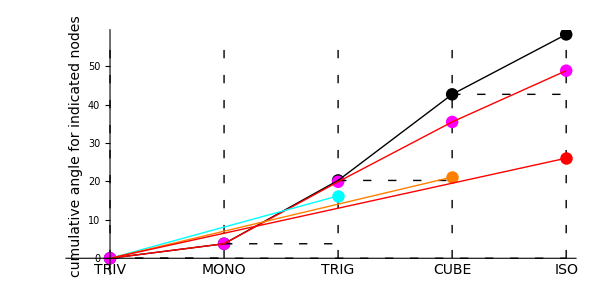

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@Range[0,nMax]];
Graphics[{PointSize[.015],
{Dashing[{.01,.02}],Line[{{0,0},{nMax,0}}],
Table[Line[{{n,0},{n,yy[nMax,Tmat,pw2]/Degree}}],{n,0,nMax}]},     (* vertical dashed lines *)
Point[{#,yy[#,Tmat,pw2]/Degree}]&/@Range[0,nMax],   (* pw2 *)
If[WantPW3=="WantPW3",
{Magenta,PointSize[.015],Point[{#,yy[#,Tmat,pw3]/Degree}]&/@Range[0,nMax]}], (* pw3 *)
{Dashing[{.01,.02}],         (* horizontal dashed steps, pw2 only*)
Line[{{#,      yy[#,Tmat,pw2]/Degree},
   {#+1,yy[#,Tmat,pw2]/Degree}}]&/@Range[0,nMax-1]},
 Line[{#,yy[#,Tmat,pw2]/Degree}&/@Range[0,nMax]],      (* the main polygonal line, pw2 *)
If[WantPW3=="WantPW3",
{Red,Line[{#,yy[#,Tmat,pw3]/Degree}&/@Range[0,nMax]]}],  (* the main polygonal line, pw3 *)
BetaSeg[#]&/@Range[2,nMax],
Text[Style[Σn[#],14],{#,-3}]&/@Range[0,nMax],
Text[Style["cumulative angle for indicated nodes",14],{-.3,.5yy[nMax,Tmat,pw2]/Degree},{0,0},{0,1}]},AspectRatio->1/2,ImageSize->600,Ticks->{None,Automatic},Axes->{None,True},AxesOrigin->{0,0}]
```

#### Difference between Pathway 2 and 3

Tmat is TmatBrownNew

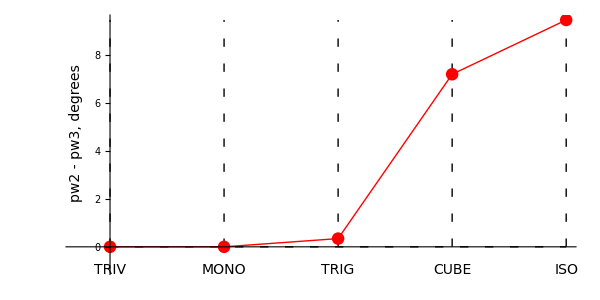

```mathematica
MatrixNote[Tmat]
Graphics[{
{Dashing[{.01,.02}],Line[{{0,0},{nMax,0}}],Table[Line[{{n,0},{n,dymax/Degree}}],{n,0,nMax}]},
{Red,PointSize[.015],Point[{#,ydiff[#,Tmat]/Degree}]&/@Range[0,nMax]}, (* points *)
{Red,Line[{#,ydiff[#,Tmat]/Degree}&/@Range[0,nMax]]},  (* line *)
Text[Style[Σn[#],14],{#,-0.1dymax/Degree}]&/@Range[0,nMax],
Text[Style["pw2 - pw3, degrees",14],{-.3,.5dymax/Degree},{0,0},{0,1}]},
AspectRatio->1/2,ImageSize->600,Ticks->{None,Automatic},Axes->{None,True},GridLines-> False,AxesOrigin->{0,0}]
```

## BrownTypo

Tmat is TmatBrownTypo

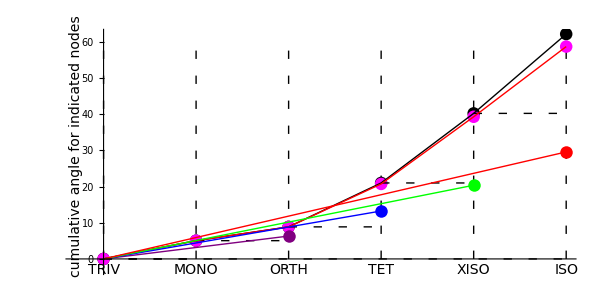

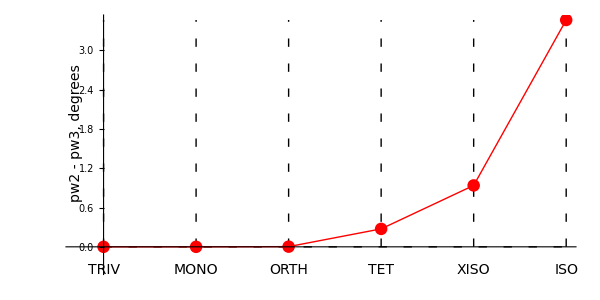

## BrownNew

Tmat is TmatBrownNew

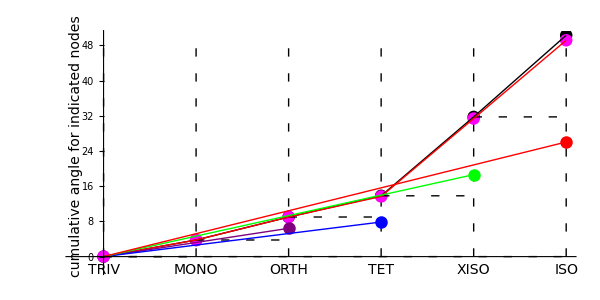

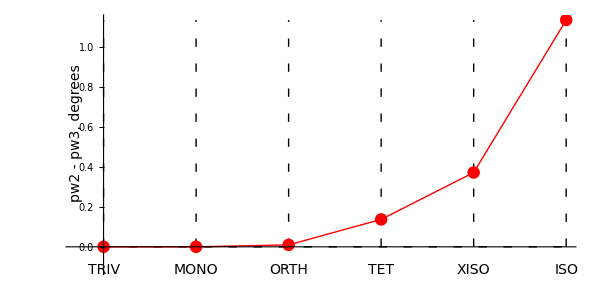

-Graphics-

-Graphics-

## SSA2023

Tmat is TmatSSA2023

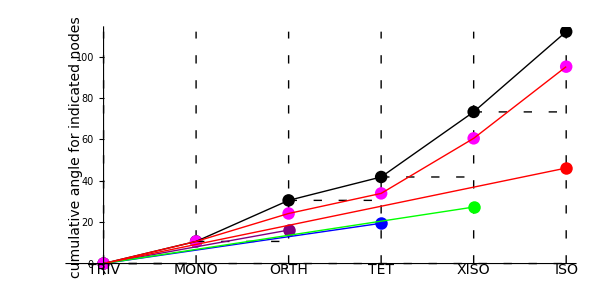

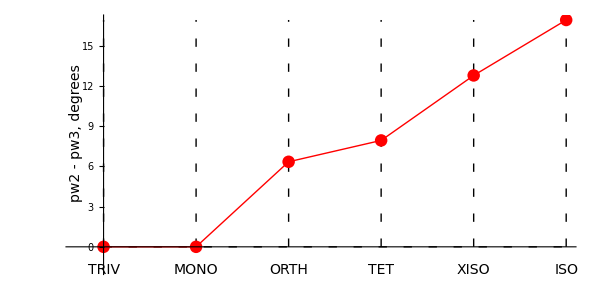

## Defeat

Tmat is TmatDefeat

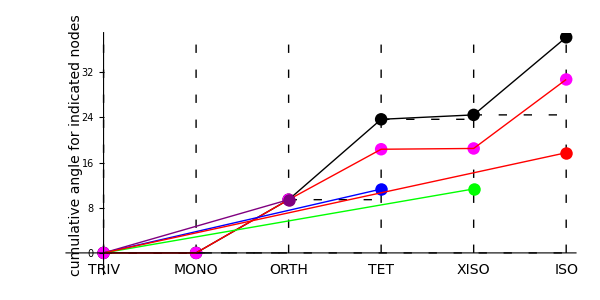

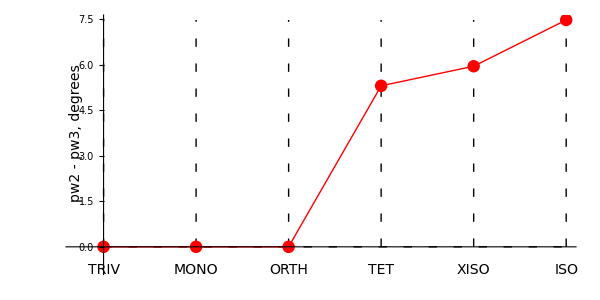

## Mar17

Tmat is TmatMar17

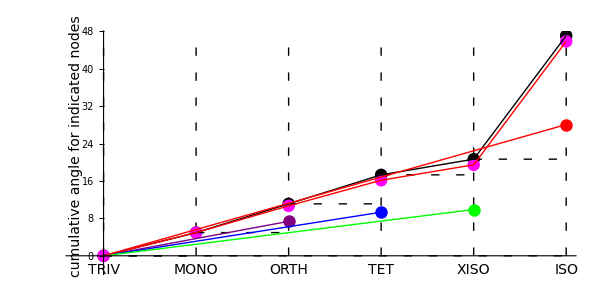

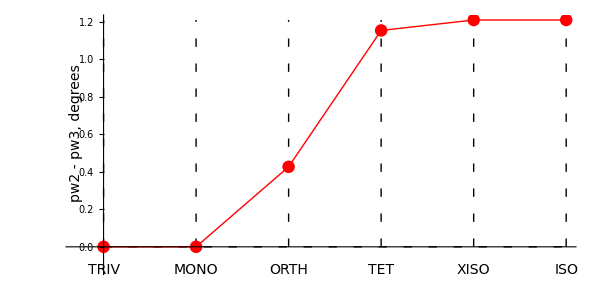

## Igel